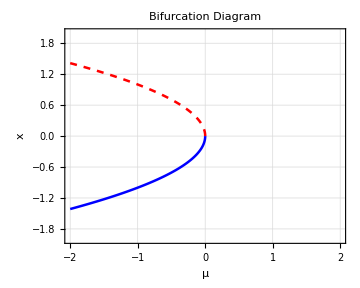

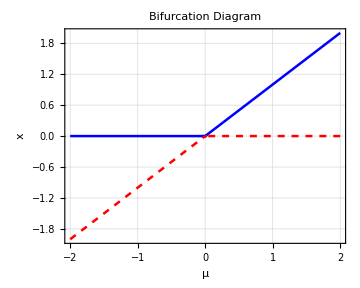

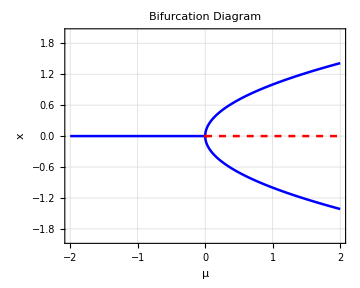

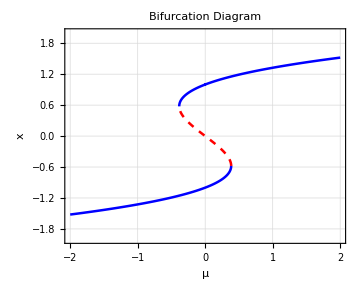

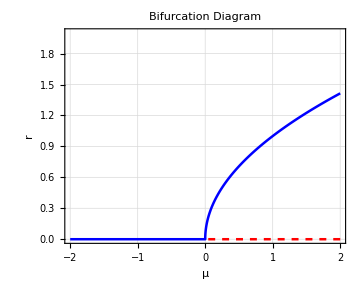

```mathematica
ClearAll[PlotBifurcation];

PlotBifurcation[f_,x_Symbol,mu_Symbol,muRange_List,xRange_List]:=Module[{dfdx,stablePlot,unstablePlot},(*1. 计算导数*)dfdx=D[f,x];
(*2. 绘制稳定分支 (df/dx<0)*)stablePlot=ContourPlot[f==0,{mu,muRange[[1]],muRange[[2]]},{x,xRange[[1]],xRange[[2]]},ContourStyle->{Blue,Thickness[0.005]},(*使用替换确保计算正确*)RegionFunction->Function[{mVal,xVal,z},(dfdx/. {mu->mVal,x->xVal})<0],PlotPoints->50,MaxRecursion->3];
(*3. 绘制不稳定分支 (df/dx>0)*)unstablePlot=ContourPlot[f==0,{mu,muRange[[1]],muRange[[2]]},{x,xRange[[1]],xRange[[2]]},ContourStyle->{Red,Dashed,Thickness[0.005]},RegionFunction->Function[{mVal,xVal,z},(dfdx/. {mu->mVal,x->xVal})>0],PlotPoints->50,MaxRecursion->3];
(*4. 合并图形并修正 PlotRange 优先级*)Show[{stablePlot,unstablePlot},Frame->True,FrameLabel->{ToString[mu],ToString[x]},PlotLabel->"Bifurcation Diagram",GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.5]],(*修正点：直接写出范围，mu 对应横轴，x 对应纵轴*)PlotRange->{muRange,xRange},ImageSize->Medium,AspectRatio->0.8]]
(*示例：跨临界分岔 (Transcritical Bifurcation)*)Clear[x,mu];
PlotBifurcation[μ+x^2,x,μ,{-2,2},{-2,2}]
PlotBifurcation[μ*x-x^2,x,μ,{-2,2},{-2,2}]
PlotBifurcation[μ*x-x^3,x,μ,{-2,2},{-2,2}]
PlotBifurcation[μ+x-x^3,x,μ,{-2,2},{-2,2}]
PlotBifurcation[μ*r-r^3,r,μ,{-2,2},{-0.0001,2}]
```

```mathematica
Clear[hopfSurface]
hopfSurface[]:=Show[{ContourPlot3D[x^2+y^2-μ==0,{x,-3,3},{μ,0,5},{y,-3,3},ContourStyle->Directive[Blue,Opacity[0.35]],Mesh->None,PlotPoints->300,BoundaryStyle->None],(*μ<0 稳定平衡*)Graphics3D[{Blue,Thick,Line[{{0,-3,0},{0,0,0}}]}],(*μ>0 不稳定平衡*)Graphics3D[{Red,Dashed,Thick,Line[{{0,0,0},{0,5,0}}]}]},Axes->True,AxesLabel->{"x","μ","y"},PlotRange->{{-3,3},{-3,5},{-3,3}},Boxed->True,ImageSize->550]

hopfSurface[]
```

-Graphics3D-

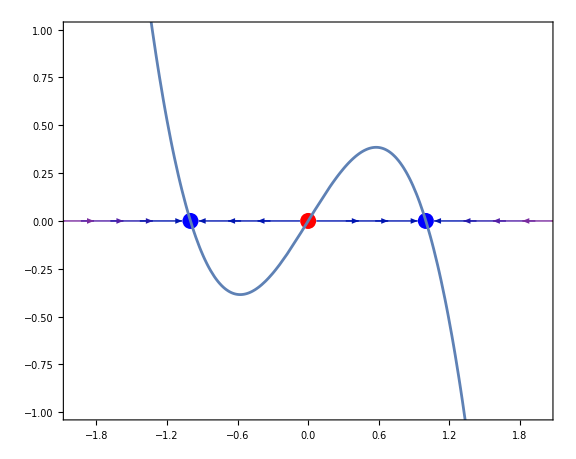

Table::iterb: 迭代器 {p,ReplaceAll[]} 没有适当的边界.

ReplaceAll::argt: `调用 `1` 时使用了 `2` 个参数；应该用 `3` 个或 `4` 个参数.

StringForm::sfq: `调用 `1` 时使用了 `2` 个参数；应该用 `3` 个或 `4` 个参数. 中有不匹配的后引号.

ReplaceAll::argt: `调用 `1` 时使用了 `2` 个参数；应该用 `3` 个或 `4` 个参数.

StringForm::sfq: `调用 `1` 时使用了 `2` 个参数；应该用 `3` 个或 `4` 个参数. 中有不匹配的后引号.

ReplaceAll::reps: {NSolve[(-x^3+x μ)[x,1]==0&&-3≤x≤3,x,]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，Table::iterb 的进一步输出将被抑制.

```mathematica
Clear[phaseLinePlot]

phaseLinePlot[f_,xRange_:{-3,3},μRange_:{-2,2}]:=Manipulate[Module[{sol,eqPts,df,stable,unstable,semiStable,xVal},(*1. 计算导数函数*)df[xVal_]:=Derivative[1,0][f][xVal,μ];
(*2. 求实数平衡点，确保返回的是列表*)sol=Quiet@NSolve[f[x,μ]==0&&xRange[[1]]<=x<=xRange[[2]],x,Reals];
(*核心修复：如果 sol 是空集，显式指定 eqPts 为空列表*)eqPts=If[sol==={},{},DeleteDuplicates[Chop[x/. sol,10^-8]]];
(*3. 分类平衡点*)stable=Select[eqPts,df[#]<0&];
unstable=Select[eqPts,df[#]>0&];
Show[{(*相线箭头*)VectorPlot[{f[x,μ],0},{x,xRange[[1]],xRange[[2]]},{y,-0.2,0.2},VectorPoints->Table[{x,0},{x,xRange[[1]],xRange[[2]],0.25}],VectorScale->{Small,0.6,None},AspectRatio->1/5,Frame->False,Axes->{True,False},AxesOrigin->{0,0}],(*绘制点：增加空列表检查，防止 Graphics 报错*)Graphics[{(*稳定点：实心蓝*)Blue,PointSize[0.02],Point[Table[{p,0},{p,stable}]],(*不稳定：空心红*)Red,PointSize[0.02],Point[Table[{p,0},{p,unstable}]]}]},PlotRange->{xRange,{-0.2,0.2}},ImageSize->Large]],{μ,μRange[[1]],μRange[[2]]}]
phaseLinePlotnoanime[f_,xRange_:{-3,3},μ_]:=Module[{sol,eqPts,df,stable,unstable,semiStable,xVal},(*1. 计算导数函数*)df[xVal_]:=Derivative[1,0][f][xVal,μ];
(*2. 求实数平衡点，确保返回的是列表*)sol=Quiet@NSolve[f[x,μ]==0&&xRange[[1]]<=x<=xRange[[2]],x,Reals];
(*核心修复：如果 sol 是空集，显式指定 eqPts 为空列表*)eqPts=If[sol==={},{},DeleteDuplicates[Chop[x/. sol,10^-8]]];
(*3. 分类平衡点*)stable=Select[eqPts,df[#]<0&];
unstable=Select[eqPts,df[#]>0&];
Show[{(*相线箭头*)VectorPlot[{f[x,μ],0},{x,xRange[[1]],xRange[[2]]},{y,-0.2,0.2},VectorPoints->Table[{x,0},{x,xRange[[1]],xRange[[2]],0.25}],VectorScale->{Small,0.6,None},AspectRatio->1/5,Frame->False,Axes->{True,False},AxesOrigin->{0,0}],(*绘制点：增加空列表检查，防止 Graphics 报错*)Graphics[{(*稳定点：实心蓝*)Blue,PointSize[0.02],Point[Table[{p,0},{p,stable}]],(*不稳定：空心红*)Red,PointSize[0.02],Point[Table[{p,0},{p,unstable}]]}]},PlotRange->{xRange,{-0.2,0.2}},ImageSize->Large]]

(*测试*)
anjie[x_,μ_]:=μ+x^2
kualinjie[x_,μ_]:=μ*x+x^2
yinchajie[x_,μ_]:=μ*x-x^3
zhihouchajie[x_,μ_]:=μ+x-x^3
Show[phaseLinePlotnoanime[yinchajie,{-3,3},1],Plot[yinchajie[x,1],{x,-3,3}],PlotRange->{{-2,2},{-1,1}},Axes->True,Frame->True,AspectRatio->0.8]
```

```mathematica
Clear[phaseLinePlot]

phaseLinePlot[f_,xRange_:{-3,3},μRange_:{-2,2}]:=Manipulate[Module[{sol,eqPts,df,stable,unstable,semiStable,xVal},(*1. 计算导数函数*)df[xVal_]:=Derivative[1,0][f][xVal,μ];
(*2. 求实数平衡点，确保返回的是列表*)sol=Quiet@NSolve[f[x,μ]==0&&xRange[[1]]<=x<=xRange[[2]],x,Reals];
(*核心修复：如果 sol 是空集，显式指定 eqPts 为空列表*)eqPts=If[sol==={},{},DeleteDuplicates[Chop[x/. sol,10^-8]]];
(*3. 分类平衡点*)stable=Select[eqPts,df[#]<0&];
unstable=Select[eqPts,df[#]>0&];
Show[{(*相线箭头*)VectorPlot[{f[x,μ],0},{x,xRange[[1]],xRange[[2]]},{y,-0.2,0.2},VectorPoints->Table[{x,0},{x,xRange[[1]],xRange[[2]],0.25}],VectorScale->{Small,0.6,None},AspectRatio->1/5,Frame->False,Axes->{True,False},AxesOrigin->{0,0}],(*绘制点：增加空列表检查，防止 Graphics 报错*)Graphics[{(*稳定点：实心蓝*)Blue,PointSize[0.02],Point[Table[{p,0},{p,stable}]],(*不稳定：空心红*)Red,PointSize[0.02],Point[Table[{p,0},{p,unstable}]]}]},PlotRange->{xRange,{-0.2,0.2}},ImageSize->Large]],{μ,μRange[[1]],μRange[[2]]}]
phaseLinePlotnoanime[f_,xRange_:{-3,3},μ_]:=Module[{sol,eqPts,df,stable,unstable,semiStable,xVal},(*1. 计算导数函数*)df[xVal_]:=Derivative[1,0][f][xVal,μ];
(*2. 求实数平衡点，确保返回的是列表*)sol=Quiet@NSolve[f[x,μ]==0&&xRange[[1]]<=x<=xRange[[2]],x,Reals];
(*核心修复：如果 sol 是空集，显式指定 eqPts 为空列表*)eqPts=If[sol==={},{},DeleteDuplicates[Chop[x/. sol,10^-8]]];
(*3. 分类平衡点*)stable=Select[eqPts,df[#]<0&];
unstable=Select[eqPts,df[#]>0&];
Show[{(*相线箭头*)VectorPlot[{f[x,μ],0},{x,xRange[[1]],xRange[[2]]},{y,-0.2,0.2},VectorPoints->Table[{x,0},{x,xRange[[1]],xRange[[2]],0.25}],VectorScale->{Medium,0.6,None},AspectRatio->1/5,Frame->False,Axes->{True,False},AxesOrigin->{0,0}],(*绘制点：增加空列表检查，防止 Graphics 报错*)Graphics[{(*稳定点：实心蓝*)Blue,PointSize[0.02],Point[Table[{p,0},{p,stable}]],(*不稳定：空心红*)Red,PointSize[0.02],Point[Table[{p,0},{p,unstable}]]}]},PlotRange->{xRange,{-0.2,0.2}},ImageSize->Large]]

(*测试*)
anjie[x_,μ_]:=μ+x^2
kualinjie[x_,μ_]:=μ*x+x^2
yinchajie[x_,μ_]:=μ*x-x^3
zhihouchajie[x_,μ_]:=μ+x-x^3
Manipulate[Show[phaseLinePlotnoanime[kualinjie,μ],Plot[kualinjie[x,μ],{x,-3,3}],PlotRange->{{-3,3},{-1,2}},AspectRatio->0.8,Axes->True,Frame->True,ImageSize->Medium],{μ,-2,2}]
(*phaseLinePlot[anjie]
phaseLinePlot[kualinjie]
phaseLinePlot[yinchajie]
phaseLinePlot[zhihouchajie]*)
```

```mathematica
color[c_,d_,x_]:=If[d-3 x^2>=0,Red,Blue]
ContourPlot3D[c+d x-x^3==0,{c,-20,20},{d,-20,20},{x,-10,10},MeshStyle->None,PlotPoints->100,AxesLabel->{"c","d","x"},ColorFunction->color]
```

-Graphics3D-

```mathematica
ContourPlot3D[c+d x-x^3==0,{c,-20,20},{d,-20,20},{x,-10,10},MeshStyle->None,PlotPoints->200,AxesLabel->{"c","d","x"},ColorFunction->Function[{c,d,x,f},If[d-3 x^2>=0,Red,Blue]],ColorFunctionScaling->False,ContourStyle->Directive[Opacity[0.8],Specularity[White,30]]]
```

-Graphics3D-

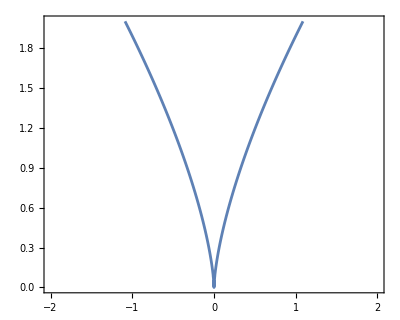

```mathematica
ContourPlot[4d^3==27c^2,{c,-2,2},{d,0,2},PlotPoints->100,AspectRatio->0.8]
```

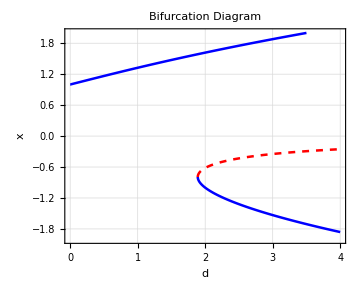

```mathematica
PlotBifurcation[1+d x-x^3,x,d,{0,4},{-2,2}]
```

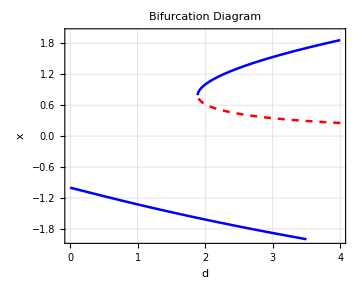

```mathematica
PlotBifurcation[-1+d x-x^3,x,d,{0,4},{-2,2}]
```

```mathematica
ContourPlot3D[c+d x-x^3==0,{c,-20,20},{d,-20,20},{x,-10,10},MeshStyle->None,PlotPoints->200,Axes->False,Boxed->False,BoxRatios->{1,1,1},ColorFunction->Function[{c,d,x,f},If[d-3 x^2>=0,Red,Blue]],ColorFunctionScaling->False,ContourStyle->Directive[Opacity[0.8],Specularity[White,30]]]
```

```mathematica
Graphics[{Text[Style["Bifurcation Theory and its Applications",FontSize->60,Bold,RGBColor[30/256, 64/256, 175/256],FontFamily->"JuliaMono ExtraBoldItalic"]]}]
```